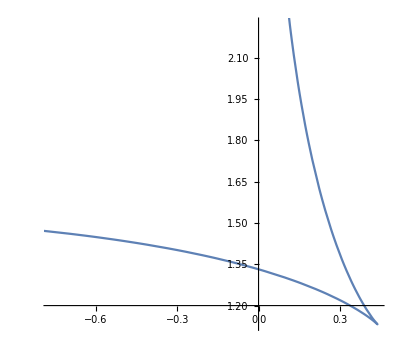

```mathematica
x=t+Log[ⅇ,Cos[t]];
y=t-Log[ⅇ,Sin[t]];
ParametricPlot[{x,y},{t,0,2Pi}]
```

```mathematica
x1=D[x,{t,1}]
```

1-Tan[t]

```mathematica
y1=D[y,{t,1}]
```

1-Cot[t]

```mathematica
y1x=y1/x1
```

(1-Cot[t])/(1-Tan[t])

```mathematica
y2x=D[y1x,{t,1}]/x1
```

(((1-Cot[t]) Sec[t]^2)/(1-Tan[t])^2+Csc[t]^2/(1-Tan[t]))/(1-Tan[t])

```mathematica
ParametricPlot[{x,y2x},{t,0,2Pi}]
```

-Graphics-